# Equipotential lines. Starter Code

#### Set up boundaries for plane and for electrodes

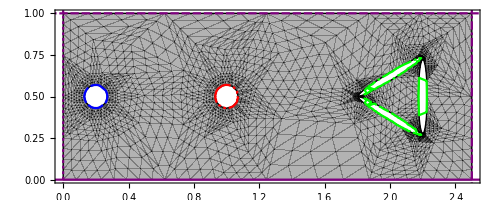

```mathematica
boundaries={
-y-0, (*boundaries[[1]]*)
y-1,(*boundaries[[2]]*)
 0-x, (*boundaries[[3]]*)
-2.5+x,(*boundaries[[4]]*)
1/200-(-0.2+x)^2-(y-0.5)^2, (*boundaries[[5]]*)
1/200-(-1+x)^2-(y-0.5)^2,(*boundaries[[6]]*)
 1/5-((x-2)Cos[π/6]+(y-0.38)Sin[π/6])^2/0.25^2-((x-2)Sin[π/6]+(y-0.38)Cos[π/6])^2/0.05^2,(*boundaries[[7]]*)
 1/5-((x-2)Cos[-π/6]+(y-0.62)Sin[-π/6])^2/0.25^2-((x-2)Sin[-π/6]+(y-0.62)Cos[-π/6])^2/0.05^2,(*boundaries[[8]]*)

 1/1.25-((x-2.2)Cos[π/2]+(y-0.5)Sin[π/2])^2/0.25^2-((x-2.2)Sin[π/2]+(y-0.5)Cos[π/2])^2/0.03^2(*boundaries[[9]]*)
};
Ω=ImplicitRegion[And@@(#≤0&/@boundaries),{x,y}];

Show[RegionPlot[Ω],
ContourPlot[Evaluate[Thread[boundaries==0]],
{x,-.1,5},{y,-0.1,2},
ContourStyle->{Purple,Purple,Purple,Purple,Blue, Red, Green, Green, Green}],AspectRatio->Automatic]
```

#### Specify voltage on boundaries

ContourPlot::cfun: Value of option ColorFunction -> Electric Potential Map is not a valid color function, or a gradient ColorData entity.

InterpolatingFunction::dmval: Input value {0.16141,0.441998} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.163027,0.44038} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.163836,0.439571} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

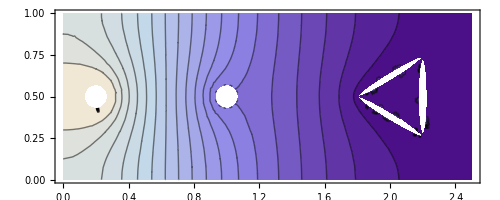

```mathematica
(* If condition for a border not given, potential can have any value there *)

sol =NDSolveValue[{∇_{x,y}^2 u[x,y]==0,
{DirichletCondition[u[x,y]==5,boundaries[[5]]==0],
DirichletCondition[u[x,y]==0,boundaries[[6]]==0],
DirichletCondition[u[x,y]==-2,boundaries[[7]]==0],
DirichletCondition[u[x,y]==-2,boundaries[[8]]==0],
DirichletCondition[u[x,y]==-2,boundaries[[9]]==0]
}},u,{x,y}∈Ω];

ContourPlot[sol[x,y],{x,y}∈Ω,Mesh->None,
ColorFunction-> "Electric Potential Map",
Contours -> 18,AspectRatio->Automatic]
```